```mathematica
(*Not the posted version of this question: http://mathematica.stackexchange.com/questions/41735/trouble-with-dynamic-range-in-setterbar, but modified with Nasser's answer*)

(*ClearAll[range]
Manipulate[
tick;
Dynamic@If[ tabNumber == dynTab,Plot[ x^2, {x, 0, 1}],Plot[ 1-x^2, {x, 0, 1}]]
,
Evaluate@With[{twiceRange = 2 range},
TabView[
{
"dynamic range"->Column[ tabNumber = dynTab ;{
Row[{Manipulator[Dynamic[m2,(m2=#;tick=Not[tick])&],{2,twiceRange,2}]," ", Dynamic[m2] }](*,
Row[{SetterBar[Dynamic[s2,(s2=#;tick=Not[tick])&],Range[twiceRange]]," ", Dynamic[s1] }]*)
}],
"static range"->Column[ tabNumber = staticTab ;{
Row[{Manipulator[Dynamic[range,(range=#;tick=Not[tick])&],{2,8,2}]," ", Dynamic[range] }],
Row[{SetterBar[Dynamic[s1,(s1=#;tick=Not[tick])&],Range[8]]," ", Dynamic[s1] }]
}]
}, Dynamic @tabNumber ] ]
,{{tick,False},None}
,{{tabNumber,1},None},{{dynTab, 1}, None},{{staticTab, 2}, None}
,{{m2, 2}, None},{{s1, 2}, None},{{s2, 2}, None}
,{{range, 4}, None}
,TrackedSymbols:>{tick},ControlPlacement->Left
, Initialization :> { (*range = 8 ;*)}
]*)

(*try with global: 
http://mathematica.stackexchange.com/questions/13658/enabled-option-for-slider-in-manipulate-not-updating-dynamically?rq=1 
*)
ClearAll[range]
Manipulate[
tick;
Dynamic@If[ tabNumber == dynTab,Plot[ x^2, {x, 0, 1}],Plot[ 1-x^2, {x, 0, 1}]]
,
Evaluate@TabView[
tabContents[ Dynamic@twiceRange ]
, Dynamic @tabNumber ] 

,{{tick,False},None}
,{{tabNumber,1},None},{{dynTab, 1}, None},{{staticTab, 2}, None}
,{{m2, 2}, None},{{s1, 2}, None},{{s2, 2}, None}

,TrackedSymbols:>{tick},ControlPlacement->Left
, Initialization :> { 
n = 4 ; twiceRange = Range[2 n] ;
tabContents[r_] :=  {
"dynamic range"->Column[ tabNumber = dynTab ;{
Row[{Manipulator[Dynamic[m2,(m2=#;tick=Not[tick])&],{2,r,2}]," ", Dynamic[m2] }],
Row[{SetterBar[Dynamic[s2,(s2=#;tick=Not[tick])&],r]," ", Dynamic[s1] }]
}],
"static range"->Column[ tabNumber = staticTab ;{
Row[{Manipulator[Dynamic[n,(n=#;tick=Not[tick])&],{2,8,2}]," ", Dynamic[n] }],
Row[{SetterBar[Dynamic[s1,(s1=#;tick=Not[tick])&],Range[8]]," ", Dynamic[s1] }]
}]
}
}
]
```

```mathematica
ClearAll[range]
Manipulate[tick;
If[tabNumber==dynTab,Plot[x^2,{x,0,1}],Plot[1-x^2,{x,0,1}]]
,TabView[{
"use n-loc as range"->Column[tabNumber=dynTab;{
"dynamic range manipulators:",
Row[{Manipulator[Dynamic[m2,(m2=#;tick=Not[tick])&],Dynamic@{1,2range}]," ",Dynamic[m2]}],Row[{Dynamic@SetterBar[Dynamic[s2,(s2=#;tick=Not[tick])&],Range[range]]," ",Dynamic[s2]}],
"",
"static range manipulators:",
Row[{Manipulator[Dynamic[m1,(m1=#;tick=Not[tick])&],{1,4}]," ",Dynamic[m1]}],Row[{SetterBar[Dynamic[s1,(s1=#;tick=Not[tick])&],Range[4]]," ",Dynamic[s1]}]
}],
"loc"->Column[tabNumber=staticTab;{
LocatorPane[ Dynamic[u,(
u = # ;
range = (Dimensions[u] // First);

tick=Not[tick])&],
Plot[x^3, {x, -1, 1}, PlotRange -> {{-1, 1}, {-1,1}}],
LocatorAutoCreate->True, 
ContinuousAction->False
] 
,Row[{"u = ", Dynamic@u}]
}]
},Dynamic@tabNumber]
,{{tick,False},None}
,{{u,{{0.5, 0.3}, {0.3, 0.9}}},None}
,{{tabNumber,1},None}
,{{dynTab,1},None}
,{{staticTab,2},None}
,{{m1,2},None}
,{{m2,2},None}
,{{s1,2},None}
,{{s2,2},None}
,{{range,2},None}
,TrackedSymbols:>{tick(*, range*)},ControlPlacement->Left
(*use a global (comment out range above to try) ... doesn't work: *)
(*, Initialization:> { range = 2 ; }*)
]
```

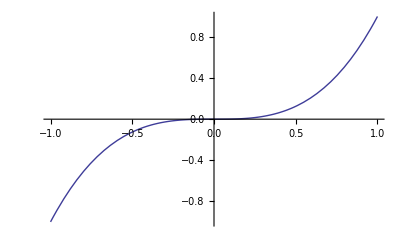

```mathematica
Plot[x^3, {x, -1, 1}, PlotRange -> {{-1, 1}, {-1,1}}]
```

```mathematica
SetterBar[2,{1,2}]
```